# Minus-K Scratch Notebook

## Max Freeman

## Initial Notes

jennifer hoffman stm damping

minus k technology stm vibration isolation scanning tunneling microscope
^ paul weiss -author of papers

Rod Lake @ UW Madison

First: Simulate vibrational spectrum of room
Next: Rod Lake’s articles

airleg/pneumatic damping profile
vibrational damping springs

first: room -> airlegs -> spring -> final
next: room -> airlegs -> minus k spring -> final

Transfer function of airlegs

Transfer function of spring

## Terminology

Stress: Force/Area = F/A

Strain: Change in Length / Length = δL/L_0

Stiffness / Modulus: how much energy must be put into the sample to distort it. E = stress/strain

Damping Capacity: a material’s ability to dissipate elastic strain energy (converting to mechanical energy to heat) during mechanical vibration  ⇒ Energy / Volume.

## Images

-Graphics-

-Graphics-

## Chamberlain Vibrational Data

```mathematica
bins = {1.25, 1.6, 2, 2.5, 3.15, 4, 5, 6.3, 8, 10, 12.5, 16, 20, 25, 31.5, 40, 50, 63, 80, 100};
pixels = {200,190, 196, 210, 230, 210, 238, 266, 285, 278,  315, 278, 264, 251, 268, 200, 152, 137, 90, 69};
```

```mathematica
f[x_]:= y/.Solve[x== 430/3(Log10[y*10^12]-2),y]⟦1,1⟧//N;
data = Table[f[pixels⟦i⟧],{i, 1, Length[pixels]}]
```

{2.48513×10^-9,2.11632×10^-9,2.33046×10^-9,2.91821×10^-9,4.02394×10^-9,2.91821×10^-9,4.57578×10^-9,7.17487×10^-9,9.73581×10^-9,8.70031×10^-9,1.57643×10^-8,8.70031×10^-9,6.94801×10^-9,5.63849×10^-9,7.40913×10^-9,2.48513×10^-9,1.14938×10^-9,9.03262×10^-10,4.24529×10^-10,3.02967×10^-10}

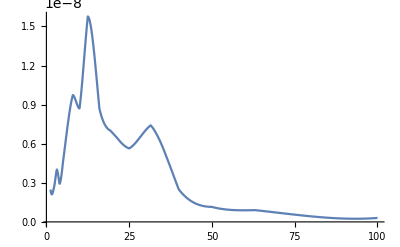

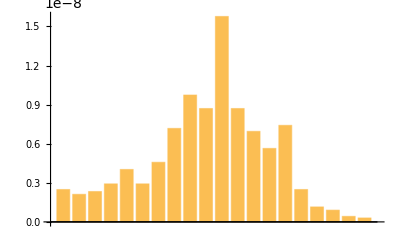

```mathematica
intfun=Interpolation[Transpose[{bins, data}]];
Plot[intfun[x], {x, 1.25, 100}]
 BarChart[data]
```

## Transfer Functions

### Damped Oscillator Transfer Function

-Graphics-